# Bifurcation Diagrams

```mathematica
{α,β,σ,n,κ,δ}=.;
Gp[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β (1/n+(n-1)/n y)]))-κ;
Gn[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β ((n-1)/n y)]));
dydt[y_,Y_,α_,β_,σ_,n_,κ_,δ_]=y(1-y)(1-Y)(Gp[y,α,β,σ,n,κ] -Gn[y,α,β,σ,n,κ]);
dYdt[y_,Y_,α_,β_,σ_,n_,κ_,δ_]=-Y(δ-(1-Y)(Gp[y,α,β,σ,n,κ] y+Gn[y,α,β,σ,n,κ](1-y)));
Y[y0_,α_,β_,σ_,n_,κ_,δ_]:=1-δ/(Gp[y0,α,β,σ,n,κ] y0+Gn[y0,α,β,σ,n,κ](1-y0));
J[y0_,Y0_,α_,β_,σ_,n_,κ_,δ_]=D[{dydt[y0,Y0,α,β,σ,n,κ,δ],dYdt[y0,Y0,α,β,σ,n,κ,δ]},{{y0,Y0}}];
stableQ1[y0_,α_,β_,σ_,n_,κ_,δ_]:=(Tr[#]<0&&Det[#]>0)&@J[y0,Y[y0,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ];
```

### Vary n

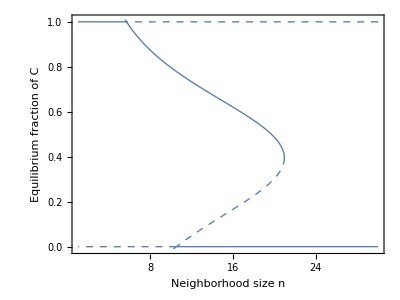

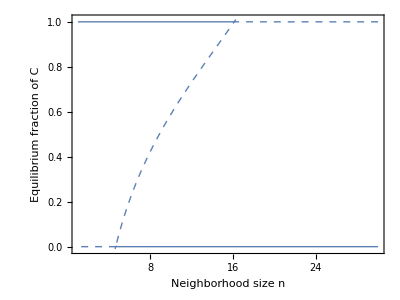

```mathematica
{α,β,σ,n,κ,δ}=.;
{α,β,σ,κ,δ}={1,5,2,0.5,0.1};
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},Not@stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Equilibrium fraction of C"}
,PlotPoints->50
],

ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Equilibrium fraction of C"}
,PlotPoints->50]
]
{α,β,σ,κ,δ}={1,2,3,0.5,0.1};
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},Not@stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Equilibrium fraction of C"}
,PlotPoints->50
],

ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{n,1,30},{y,-0.01,1.01}
,RegionFunction-> Function[{n,y},stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.75
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Neighborhood size n","Equilibrium fraction of C"}
,PlotPoints->50]
]
```

## Vary benefit parameter β

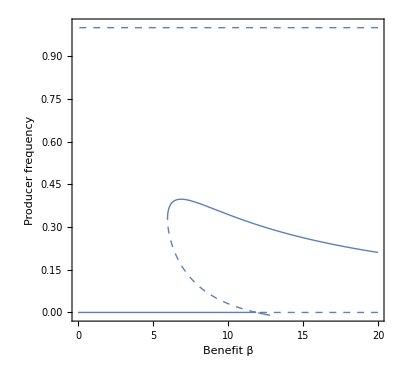

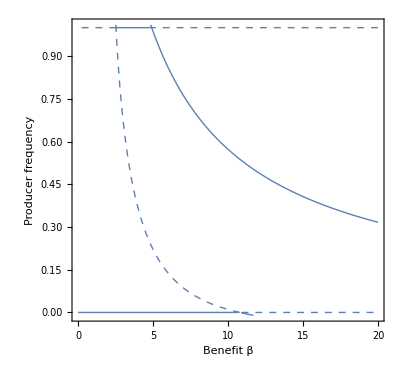

```mathematica
{α,β,σ,n,κ,δ}=.;
{α,σ,n,κ,δ}={1,2,25,0.5,0.1};
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{β,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},Not@stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
,
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{β,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
]
{α,σ,n,κ,δ}={1,3,25,0.5,0.1};
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{β,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},Not@stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
,
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{β,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
]
```

```mathematica
{dydt[y0,Y0,α,β,σ,n,κ,δ],dYdt[y0,Y0,α,β,σ,n,κ,δ]}
```

{(1-y0) y0 (1-Y0) (-((1+ⅇ^σ) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))+((1+ⅇ^σ) α)/(1+ⅇ^(-(1/n+((-1+n) y0)/n) β+σ))-κ),-Y0 (δ-(1-Y0) (((1+ⅇ^σ) (1-y0) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))+y0 (((1+ⅇ^σ) α)/(1+ⅇ^(-(1/n+((-1+n) y0)/n) β+σ))-κ)))}

```mathematica
Solve[δ-(1-Y0) (((1+ⅇ^σ) (1-y0) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))+y0 (((1+ⅇ^σ) α)/(1+ⅇ^(-(1/n+((-1+n) y0)/n) β+σ))-κ))==0,Y0]
```

{{Y0→(((1+ⅇ^σ) (1-y0) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))-δ+y0 (((1+ⅇ^σ) α)/(1+ⅇ^((-1/n-((-1+n) y0)/n) β+σ))-κ))/(((1+ⅇ^σ) (1-y0) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))+y0 (((1+ⅇ^σ) α)/(1+ⅇ^((-1/n-((-1+n) y0)/n) β+σ))-κ))}}

## Vary benefit parameter σ

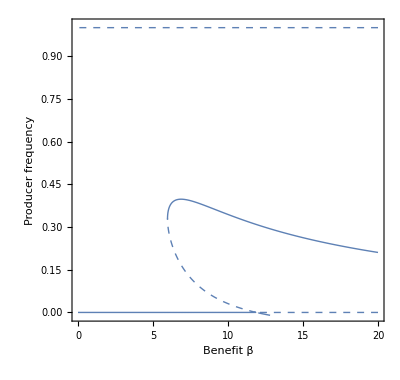

```mathematica
{α,β,σ,n,κ,δ}=.;
{α,σ,n,κ,δ}={1,2,5,0.5,0.1};
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{σ,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},Not@stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
,
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{σ,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
]
(*{α,σ,n,κ,δ}={1,3,25,0.5,0.1};
Show[
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{β,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},Not@stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick,Dashed}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
,
ContourPlot[dydt[y,Y[y,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ]==0
,{β,0,20},{y,-0.01,1.01}
,RegionFunction-> Function[{β,y},stableQ1[y,α,β,σ,n,κ,δ]]
,ContourStyle-> {Thick}
,ImageSize->400(*Larger Size => Better Quality of PDF*)
,LabelStyle->{FontSize->20,Black,FontFamily->"Arial"}(*Can also choose "Helvetica", or "Times"*)
,FrameTicks->{{All,None},{All,None}}
,AspectRatio->0.95
,FrameStyle->Directive[Thickness[0.0025],Black]
,Axes->{True,False}
,FrameLabel->{"Benefit β","Producer frequency"}
,PlotPoints->100]
]*)
```

```mathematica
{dydt[y0,Y0,α,β,σ,n,κ,δ],dYdt[y0,Y0,α,β,σ,n,κ,δ]}
```

{(1-y0) y0 (1-Y0) (-((1+ⅇ^σ) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))+((1+ⅇ^σ) α)/(1+ⅇ^(-(1/n+((-1+n) y0)/n) β+σ))-κ),-Y0 (δ-(1-Y0) (((1+ⅇ^σ) (1-y0) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))+y0 (((1+ⅇ^σ) α)/(1+ⅇ^(-(1/n+((-1+n) y0)/n) β+σ))-κ)))}

```mathematica
Solve[δ-(1-Y0) (((1+ⅇ^σ) (1-y0) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))+y0 (((1+ⅇ^σ) α)/(1+ⅇ^(-(1/n+((-1+n) y0)/n) β+σ))-κ))==0,Y0]
```

{{Y0→(((1+ⅇ^σ) (1-y0) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))-δ+y0 (((1+ⅇ^σ) α)/(1+ⅇ^((-1/n-((-1+n) y0)/n) β+σ))-κ))/(((1+ⅇ^σ) (1-y0) α)/(1+ⅇ^(-((-1+n) y0 β)/n+σ))+y0 (((1+ⅇ^σ) α)/(1+ⅇ^((-1/n-((-1+n) y0)/n) β+σ))-κ))}}

```mathematica
{α,β,σ,n,κ,δ}=.;
Gp[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β (1/n+(n-1)/n y)]))+α(1+Exp[σ])(ⅇ^(((1+(-1+n) y) β)/n+σ) (-ⅇ^(((1+(-1+n) y) β)/n)+ⅇ^σ) β^2(n-1)y(1-y))/(2(ⅇ^(((1+(-1+n) y) β)/n)+ⅇ^σ)^3 n^2)-κ;
Gn[y_,α_,β_,σ_,n_,κ_]:=α ((1+Exp[σ])/(1+Exp[σ-β ((n-1)/n y)]))+α(1+Exp[σ])(ⅇ^((((-1+n) y) β)/n+σ) (-ⅇ^((((-1+n) y) β)/n)+ⅇ^σ) β^2(n-1)y(1-y))/(2(ⅇ^((((-1+n) y) β)/n)+ⅇ^σ)^3 n^2);
dydt[y_,Y_,α_,β_,σ_,n_,κ_,δ_]=y(1-y)(1-Y)(Gp[y,α,β,σ,n,κ] -Gn[y,α,β,σ,n,κ]);
dYdt[y_,Y_,α_,β_,σ_,n_,κ_,δ_]=-Y(δ-(1-Y)(Gp[y,α,β,σ,n,κ] y+Gn[y,α,β,σ,n,κ](1-y)));
Y[y0_,α_,β_,σ_,n_,κ_,δ_]:=1-δ/(Gp[y0,α,β,σ,n,κ] y0+Gn[y0,α,β,σ,n,κ](1-y0));
J[y0_,Y0_,α_,β_,σ_,n_,κ_,δ_]=D[{dydt[y0,Y0,α,β,σ,n,κ,δ],dYdt[y0,Y0,α,β,σ,n,κ,δ]},{{y0,Y0}}];
stableQ1[y0_,α_,β_,σ_,n_,κ_,δ_]:=(Tr[#]<0&&Det[#]>0)&@J[y0,Y[y0,α,β,σ,n,κ,δ],α,β,σ,n,κ,δ];
```